# Evolutionary Dynamics Ch.2:

## 2.1 Reproduction

```mathematica
(*exponential growth difference equation*)
```

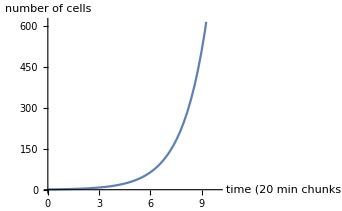

```mathematica
Plot[1*2^t,{t,0,10},AxesLabel->{"time (20 min chunks)","number of cells"}]
```

```mathematica
(*differential equation version of exponential difference equation. 5/36 is because ten 20 minute chunks is 5/36 of a day. rate of 72 means that there are an average of 72 cell divisions in a day, ie; 1440/x=20 and  then x=72*)
```

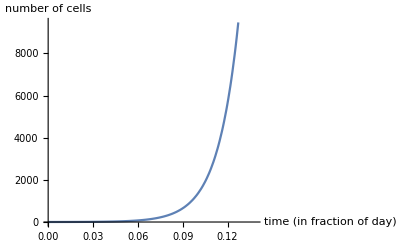

```mathematica
Plot[1*ⅇ^(72 t),{t,0,5/36},AxesLabel->{"time (in fraction of day)","number of cells"}]
```

```mathematica
(*Deterministic Chaos: 2.1.1*)
```

```mathematica
logGrowth[x0_,r_,k_,t_]:=(k*x0*ⅇ^(r*t))/(k+x0*(ⅇ^(r*t)-1));
```

```mathematica
logDiff[a_,x_]:=a*x*(1-x);
```

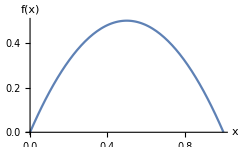

```mathematica
Plot[logDiff[#,x]&@2,{x,0,1},AxesLabel->{"x","f(x)"}]
```

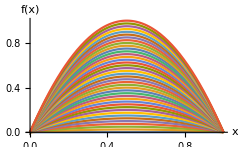

```mathematica
Plot[Evaluate[Table[logDiff[a,x],{a,0,4,0.1}]],{x,0,1},AxesLabel->{"x","f(x)"}]
```

## 2.2 Selection